```mathematica
Needs["DatabaseLink`"];
JDBCDrivers["SQLite"];
conn = OpenSQLConnection[JDBC["SQLite", "/Users/erinhengel/Dropbox/Readability/dta/read.db"]];
font="Optima";
```

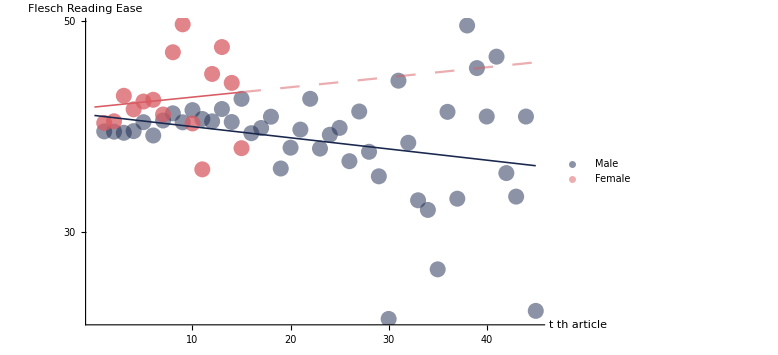

```mathematica
sql="
SELECT  t1.Sex,
(SELECT COUNT(t2.ArticleID)
	FROM (
		SELECT ArticleID, AuthorID, PubDate, Journal, FirstPage
			FROM AuthorCorr
			NATURAL JOIN Article
			WHERE Journal <>'P&P'
	) AS t2
	WHERE
		CASE
			WHEN t2.PubDate = t1.PubDate			
			THEN
				CASE
					WHEN t2.Journal = t1.Journal
					THEN t2.FirstPage >= t1.FirstPage
					ELSE t2.Journal >= t1.Journal
				END
			ELSE t2.PubDate <= t1.PubDate
		 END AND
		t2.AuthorID = t1.AuthorID
) AS PubCount, AVG(StatValue)
FROM (
	SELECT ArticleID, AuthorID, PubDate, Journal, FirstPage, Sex
		FROM AuthorCorr
		NATURAL JOIN Article
		NATURAL JOIN Author
		WHERE Journal <>'P&P'
) AS t1
NATURAL JOIN ReadStat
WHERE StatName = 'flesch_score'
GROUP BY Sex, PubCount
";
data=SQLExecute[conn,sql];
male=Select[data,#⟦1⟧==1&]⟦All,2;;⟧;
female=Select[data,#⟦1⟧==0&]⟦All,2;;⟧;
pointsize=PointSize[0.02];
thickness=Thickness[0.002];
{blue,pink}={RGBColor[26/255,40/255,78/255],RGBColor[216/255,92/255,99/255]};
legend=PointLegend[{blue,pink},{"Male","Female"},
LegendMarkers->Graphics[{EdgeForm[None],Opacity[0.5],Disk[]}],
LegendMarkerSize->12,
LabelStyle->{FontSize->16,FontColor->Gray,FontFamily->font},
LegendMargins->5,
LegendLayout->"Row"
];
MaleScatter=ListPlot[male,
PlotStyle->{blue,Opacity[0.5],pointsize}
];
MaleLine=Fit[male,{1,x},x];
MaleLinePlot=Plot[MaleLine,{x,0,Max@male⟦All,1⟧},
PlotStyle->{blue,thickness}
];
FemaleScatter=ListPlot[female,
PlotStyle->{pink,Opacity[0.75],pointsize}
];
FemaleLine=Fit[female,{1,x},x];
FemaleLinePlot=Plot[{
If[x≤Max@female⟦All,1⟧,FemaleLine],
If[x>Max@female⟦All,1⟧,FemaleLine]},
{x,0,Max@male⟦All,1⟧},
PlotStyle->{{pink,thickness}, {pink,Dashing[Large],Opacity[0.5]}},
PlotLegends->Placed[legend,{Right,Bottom}]
];
plot=Show[{MaleScatter,FemaleScatter,MaleLinePlot,FemaleLinePlot},
PlotRange->All,
AxesStyle->Directive[Thin,Gray,FontFamily->font,FontSize->Medium],
AxesOrigin->{0,0},
Ticks->{{10,20,30,40},{10,30,50}},
AxesLabel->{"
StyleBox[\"t\",\nStripOnInput->False,\nFontSlant->Italic]
StyleBox[\" \",\nStripOnInput->False,\nFontSlant->Italic]th\narticle","Flesch Reading Ease"},
LabelStyle->{FontSize->14},
ImageSize->Full
];
Export["/Users/erinhengel/Dropbox/Readability/draft/pdf/figure3.pdf",plot];
Show[plot,ImageSize->Large]
```

```mathematica
Select[male,#⟦1⟧≤15&]
```

{{1,39.5337},{2,39.5077},{3,39.4032},{4,39.56},{5,40.4047},{6,39.148},{7,40.5624},{8,41.2397},{9,40.3934},{10,41.5446},{11,40.7092},{12,40.4832},{13,41.6495},{14,40.4202},{15,42.6093}}

```mathematica
female
```

{{1,40.3296},{2,40.4878},{3,42.8984},{4,41.6187},{5,42.3542},{6,42.5204},{7,41.1305},{8,47.0073},{9,49.6448},{10,40.2847},{11,35.949},{12,44.9599},{13,47.4997},{14,44.114},{15,37.95}}